```mathematica
theta[j_,K_]:=ArcSin[K/j];
thTable[j_]:=Table[{k,theta[j,k]},{k,1/2,j,1}];
```

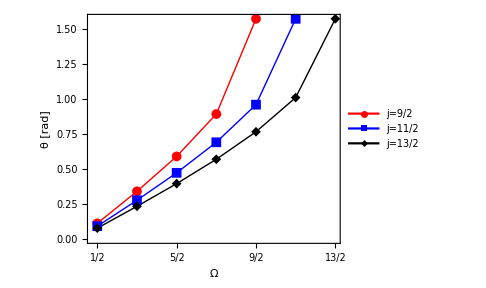

```mathematica
ListPlot[{thTable[9/2],thTable[11/2],thTable[13/2]},AspectRatio->0.8,Frame->True,Axes->False,Joined->True,ImageSize->Medium,PlotMarkers->{Automatic, Medium},PlotRange->Full,FrameStyle->Directive[Black,Thick],FrameLabel->{"Ω","θ [rad]"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},LabelStyle->{19,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"j=9/2","j=11/2","j=13/2"},{0.2,0.7}],FrameTicks->{{Automatic,Automatic},{{1/2,3/2,5/2,7/2,9/2,11/2,13/2},Automatic}}]
```